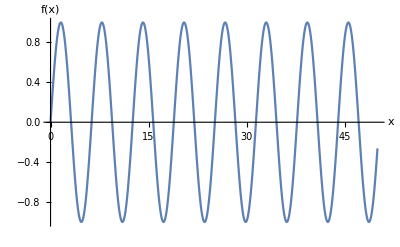

```mathematica
(*Define your function;for example,f(x)=sin(x)*)f[x_]:=Sin[x]

(*Generate the sample of the function*)
dt=0.1;
xValues=Range[0,50,dt];
yValues=f/@xValues;

(*Plot the entire discretized function*)
ListLinePlot[Transpose[{xValues,yValues}],AxesLabel->{"x","f(x)"},PlotRange->All]
```

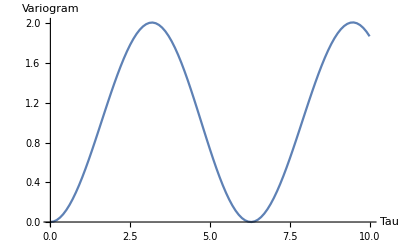

```mathematica
(*Calculate the variogram*)variogram[tau_,data_]:=Module[{Ntau,sum},Ntau=Length[data]-tau;
sum=Total[(data[[Range[1,Ntau]]]-data[[Range[1+tau,Ntau+tau]]])^2];
sum/(Ntau)]

(*Calculate and store variogram values from 0 to 10*)
variogramValues=Table[variogram[Round[tau/dt],yValues],{tau,0,10,0.1}];

(*Plot the variogram*)
ListLinePlot[variogramValues,DataRange->{0,10},AxesLabel->{"Tau","Variogram"},PlotRange->All]
```

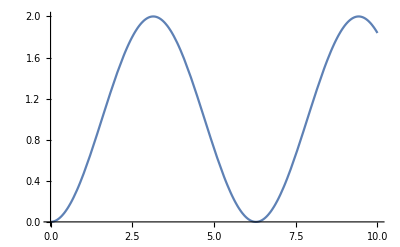

```mathematica
Plot[2*Sin[t/2]^2,{t,0,10}]
```